```mathematica
Quit[]
```

This notebook requires MaTeX which is a free package for plotting with latex fonts. Please, refer to:

```mathematica
Hyperlink["https://github.com/szhorvat/MaTeX"]
```

https://github.com/szhorvat/MaTeX

```mathematica
<<MaTeX`
```

# HDES: Designer in Horndeski (ST) Theory

### Package Definitions

Charge the xPand package

```mathematica
Block[{Print},<<xAct`xPand`];
$DefInfoQ=False;
```

Several needed definitions, like the manifold and the FLRW metric

```mathematica
DefManifold[M,4,{α,β,γ,η,κ,λ,μ,ν,σ,τ}]
DefMetric[-1,g[-μ,-ν],CD,{";","∇"},PrintAs->"g"]
Block[{Print},SetSlicing[g,n,h,cd,{"|","∂"},"FLFlat"]]; (* Flat FLRW *)
DefMetricFields[g,δg,h];
DefMatterFields[u,δu,h];
MyToxPand[expr_,gauge_,order_]:=ToxPand[expr,δg,u,δu,h, gauge,order]
org[expr_]:=NoScalar@Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
Protect[IndexForm];
PrintAs[ϕh]^="Φ"; (* Gravitational Potential *)
PrintAs[ψh]^="Ψ";
PrintAs[Eth]^="h"; (* Tensor Modes *)
$ConformalTime=False; (* Cosmic Time *)
$FirstOrderVectorPerturbations=False; (* No Vector Perturbations *)
$FirstOrderTensorPerturbations=False; (* No Tensor Perturbations *)
```

Notation for the free-functions

```mathematica
DefScalarFunction[G2,PrintAs->"G_2"];
DefScalarFunction[G2φ,PrintAs->"G_(2  φ)"];
DefScalarFunction[G2X1,PrintAs->"G_(2 SubscriptBox[X, 1])"];
DefScalarFunction[G2φX1,PrintAs->"G_(2 SubscriptBox[φX, 1])"];
DefScalarFunction[G2X1X1,PrintAs->"G_(2 SubscriptBox[X, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G2φφ,PrintAs->"G_(2  φφ)"];
DefScalarFunction[G2φφX1,PrintAs->"G_(2 SubscriptBox[φφX, 1])"];
DefScalarFunction[G2φX1X1,PrintAs->"G_(2 SubscriptBox[φX, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G2X1X1X1,PrintAs->"G_(2 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 1])"];

DefScalarFunction[G3,PrintAs->"G_3"];
DefScalarFunction[G3φ,PrintAs->"G_(3  φ)"];
DefScalarFunction[G3X1,PrintAs->"G_(3 SubscriptBox[X, 1])"];
DefScalarFunction[G3φφ,PrintAs->"G_(3  φφ)"];
DefScalarFunction[G3φX1,PrintAs->"G_(3 SubscriptBox[φX, 1])"];
DefScalarFunction[G3X1X1,PrintAs->"G_(3 SubscriptBox[X, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G3φφφ,PrintAs->"G_(3  φφφ)"];
DefScalarFunction[G3φφX1,PrintAs->"G_(3 SubscriptBox[φφX, 1])"];
DefScalarFunction[G3φX1X1,PrintAs->"G_(3 SubscriptBox[φX, 1] SubscriptBox[X, 1])"];
DefScalarFunction[G3X1X1X1,PrintAs->"G_(3 SubscriptBox[X, 1] SubscriptBox[X, 1] SubscriptBox[X, 1])"];

DefScalarFunction[G4,PrintAs->"G_4"];
DefScalarFunction[G4φ,PrintAs->"G_(4  φ)"];
DefScalarFunction[G4φφ,PrintAs->"G_(4  φφ)"];
DefScalarFunction[G4φφφ,PrintAs->"G_(4  φφφ)"];

DefScalarFunction[H0,PrintAs->"H_0"];
DefScalarFunction[ρm,PrintAs->"ρ_m"];
DefScalarFunction[Ωm,PrintAs->"Ω_m"];
DefScalarFunction[ΩΛ,PrintAs->"Ω_Λ"];
DefScalarFunction[Ωm0,PrintAs->"Ω_m0"];
DefScalarFunction[X1,PrintAs->"X_1"];
DefScalarFunction[X0,PrintAs->"X_0"];

ETensor=MyToxPand[EinsteinCD[-μ,-ν],"NewtonGauge",1];
G00=ExtractOrder[ExtractComponents[ETensor,h,{"Time","Time"}],0]//Simplify
Gij=ExtractOrder[ExtractComponents[ETensor,h,{"Space","Space"}],0]//Simplify
δG00=ExtractOrder[ExtractComponents[ETensor,h,{"Time","Time"}],1]
δG0i=ExtractOrder[ExtractComponents[ETensor,h,{"Time","Space"}],1]
δGij=Collect[ExtractOrder[ExtractComponents[ETensor,h,{"Space","Space"}],1]//Expand,{{h^-, {{, }, {μ, ν}}}}]

VisualizeTensor[MyToxPand[g[-μ,-ν],"NewtonGauge",1],h]
```

3 (H^)^2

-(a^)^2 h^- |   |  
μ | ν (3 (H^)^2+2 Ḣ)

-6 H^ (^(1)Ψ̇)+(2 ∂_α ∂^α ^(1)Ψ^)/((a^)^2)

2 (H^ ∂_ν ^(1)Φ^+∂_ν ^(1)Ψ̇)

h^- |   |  
μ | ν (6 (a^)^2 (H^)^2 (^(1)Φ^)+4 (a^)^2 Ḣ (^(1)Φ^)+2 (a^)^2 H^ (^(1)Φ̇)+6 (a^)^2 (H^)^2 (^(1)Ψ^)+4 (a^)^2 Ḣ (^(1)Ψ^)+6 (a^)^2 H^ (^(1)Ψ̇)+2 (a^)^2 (^(1)Ψ^(..))+∂_α ∂^α ^(1)Φ^-∂_α ∂^α ^(1)Ψ^)-∂_ν ∂_μ ^(1)Φ^+∂_ν ∂_μ ^(1)Ψ^

| n | h
n | -1-2 ϵ (^(1)Φ^) | 0
h | 0 | (a^)^2 h^- |   |  
μ | ν-2 ϵ (a^)^2 h^- |   |  
μ | ν (^(1)Ψ^)

We are using the following metric

Bayron: ds^2=-(1+2Φ)dt^2+a^2(1-2Ψ)δ_ij dx^i dx^j

In order to compare with 1904.06294 [astro-ph.CO], take into account that they use

Wilmar: ds^2=-(1+2Ψ)dt^2+a^2(1+2Φ)δ_ij dx^i dx^j

and therefore

ΨW=ΦB, ΦW=-ΨB

In the following, we consider two cases in the designer procedure. Firstly, we do not eliminate H and its derivative in the equations. Second, we do eliminate H and its derivative, hence we apply the sub-horizon approximation. The designer procedure is the same for both cases.

## Designer Procedure

Friedman equation and scalar field EoM (see 1904.06294 [astro-ph.CO])

```mathematica
Eq1=-(H^)^2-G2/3+H0^2*Ωm0*ah[]^-3+2/3 X1*G2X1+2 √2 X1^(3/2)*H^*G3X1;
Eq2=J/((a^)^3)-6X1*H^*G3X1-√2 X1^(1/2)G2X1;
```

These are Eqs. (162), and (163) in 1904.06294 [astro-ph.CO]

Solution for G_2 and G_(3 X_1)

```mathematica
Solve[{Eq1==0,Eq2==0},{G2,G3X1}][[1]]//Expand
```

{G_2→(√2 J √X_1)/((a^)^3)+(3 H_0^2 Ω_m0)/((a^)^3)-3 (H^)^2,G_(3 X_1)→-(G_(2 X_1))/(3 √2 √X_1 H^)+J/(6 X_1 (a^)^3 H^)}

Replacing  ΛCDM→ G_2

```mathematica
((√2 J √Subscript[X, 1])/((a^)^3)+(3 Subscript[H, 0]^2 Subscript[Ω, m0])/((a^)^3)-3 (H^)^2)/.1/((a^)^3)->((H^)^2)/(H0^2*Ωm0)-ΩΛ/Ωm0//Expand
```

-3 H_0^2 Ω_Λ-(√2 J √X_1 Ω_Λ)/Ω_m0+(√2 J √X_1 (H^)^2)/(H_0^2 Ω_m0)

This is the first equation in Eq. (164) in 1904.06294 [astro-ph.CO]

Derivative of  G_2

```mathematica
D[-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]+(√2 J √Subscript[X, 1] (H^)^2)/(Subscript[H, 0]^2 Subscript[Ω, m0])/.Hh[]->HX1[X1],X1]/.HX1[X1]->H^/.HX1'[X1]->H^'
```

-(J Ω_Λ)/(√2 √X_1 Ω_m0)+(J (H^)^2)/(√2 H_0^2 √X_1 Ω_m0)+(2 √2 J √X_1 H^ H^')/(H_0^2 Ω_m0)

Replace in G_(3 X_1)

```mathematica
-Subscript[G, 2 Subscript[X, 1]]/(3 √2 √Subscript[X, 1] H^)+J/(6 Subscript[X, 1] (a^)^3 H^)/.Subscript[G, 2 Subscript[X, 1]]->-(J Subscript[Ω, Λ])/(√2 √Subscript[X, 1] Subscript[Ω, m0])+(J (H^)^2)/(√2 Subscript[H, 0]^2 √Subscript[X, 1] Subscript[Ω, m0])+(2 √2 J √Subscript[X, 1] H^ H^')/(Subscript[H, 0]^2 Subscript[Ω, m0])/.1/((a^)^3)->((H^)^2)/(H0^2*Ωm0)-ΩΛ/Ωm0//Expand
```

-(2 J H^')/(3 H_0^2 Ω_m0)

This is the second equation in Eq. (164) in 1904.06294 [astro-ph.CO]

Integrate to get  G_3

```mathematica
Integrate[-(2 J H^')/(3 Subscript[H, 0]^2 Subscript[Ω, m0])/.H^'->HX1'[X1],X1]/.HX1[X1]->H^
```

-(2 J H^)/(3 H_0^2 Ω_m0)

## Designer Functions: HDES

```mathematica
G2->-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]+(√2 J √Subscript[X, 1] (H^)^2)/(Subscript[H, 0]^2 Subscript[Ω, m0])/.Hh[]->(X0/X1)^(1/n)
G3->-(2 J H^)/(3 Subscript[H, 0]^2 Subscript[Ω, m0])/.H^->(X0/X1)^(1/n)
```

G_2→(√2 J (X_0/X_1)^(2/n) √X_1)/(H_0^2 Ω_m0)-3 H_0^2 Ω_Λ-(√2 J √X_1 Ω_Λ)/Ω_m0

G_3→-(2 J (X_0/X_1)^(1/n))/(3 H_0^2 Ω_m0)

These are the equations in Eq. (169) in 1904.06294 [astro-ph.CO]

```mathematica
G2X1->D[-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]+(√2 J √Subscript[X, 1] (H^)^2)/(Subscript[H, 0]^2 Subscript[Ω, m0])/.Hh[]->(X0/X1)^(1/n),X1]//Simplify
G3X1->D[-(2 J (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),X1]//Simplify
```

G_(2 X_1)→(J (-4 (X_0/X_1)^(2/n)+n ((X_0/X_1)^(2/n)-H_0^2 Ω_Λ)))/(√2 H_0^2 n √X_1 Ω_m0)

G_(3 X_1)→(2 J (X_0/X_1)^(1/n))/(3 H_0^2 n X_1 Ω_m0)

```mathematica
G2X1X1->D[D[-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]+(√2 J √Subscript[X, 1] (H^)^2)/(Subscript[H, 0]^2 Subscript[Ω, m0])/.Hh[]->(X0/X1)^(1/n),X1],X1]//Simplify
G3X1X1->D[D[-(2 J (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),X1],X1]//Simplify
```

G_(2 X_1 X_1)→(J (16 (X_0/X_1)^(2/n)+n^2 (-(X_0/X_1)^(2/n)+H_0^2 Ω_Λ)))/(2 √2 H_0^2 n^2 X_1^(3/2) Ω_m0)

G_(3 X_1 X_1)→-(2 J (1+n) (X_0/X_1)^(1/n))/(3 H_0^2 n^2 X_1^2 Ω_m0)

```mathematica
G2X1X1X1->D[D[D[-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0]+(√2 J √Subscript[X, 1] (H^)^2)/(Subscript[H, 0]^2 Subscript[Ω, m0])/.Hh[]->(X0/X1)^(1/n),X1],X1],X1]//Simplify
G3X1X1X1->D[D[D[-(2 J (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),X1],X1],X1]//Simplify
```

G_(2 X_1 X_1 X_1)→(J (-64 (X_0/X_1)^(2/n)-48 n (X_0/X_1)^(2/n)+4 n^2 (X_0/X_1)^(2/n)+3 n^3 ((X_0/X_1)^(2/n)-H_0^2 Ω_Λ)))/(4 √2 H_0^2 n^3 X_1^(5/2) Ω_m0)

G_(3 X_1 X_1 X_1)→(2 J (1+3 n+2 n^2) (X_0/X_1)^(1/n))/(3 H_0^2 n^3 X_1^3 Ω_m0)

We are considering shift-symmetric theories: φ→φ+constant

```mathematica
HDESφ={Subscript[G, 2  φ]->0,Subscript[G, 2  φφ]->0,Subscript[G, 2 Subscript[φX, 1]]->0,Subscript[G, 2 Subscript[φφX, 1]]->0,Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]]->0,Subscript[G, 3  φ]->0,Subscript[G, 3  φφ]->0,Subscript[G, 3 Subscript[φX, 1]]->0,Subscript[G, 3  φφφ]->0,Subscript[G, 3 Subscript[φφX, 1]]->0,Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]]->0,Subscript[G, 4]->1/(2κ),Subscript[G, 4  φ]->0,Subscript[G, 4  φφ]->0,Subscript[G, 4  φφφ]->0};
HDESI={Subscript[G, 2]->(√2 J (Subscript[X, 0]/Subscript[X, 1])^(2/n) √Subscript[X, 1])/(Subscript[H, 0]^2 Subscript[Ω, m0])-3 Subscript[H, 0]^2 Subscript[Ω, Λ]-(√2 J √Subscript[X, 1] Subscript[Ω, Λ])/Subscript[Ω, m0],Subscript[G, 3]->-(2 J (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 Subscript[Ω, m0]),Subscript[G, 2 Subscript[X, 1]]->(J (-4 (Subscript[X, 0]/Subscript[X, 1])^(2/n)+n ((Subscript[X, 0]/Subscript[X, 1])^(2/n)-Subscript[H, 0]^2 Subscript[Ω, Λ])))/(√2 Subscript[H, 0]^2 n √Subscript[X, 1] Subscript[Ω, m0]),Subscript[G, 3 Subscript[X, 1]]->(2 J (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 n Subscript[X, 1] Subscript[Ω, m0]),Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]]->(J (16 (Subscript[X, 0]/Subscript[X, 1])^(2/n)+n^2 (-(Subscript[X, 0]/Subscript[X, 1])^(2/n)+Subscript[H, 0]^2 Subscript[Ω, Λ])))/(2 √2 Subscript[H, 0]^2 n^2 Subscript[X, 1]^(3/2) Subscript[Ω, m0]),Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]]->-(2 J (1+n) (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 n^2 Subscript[X, 1]^2 Subscript[Ω, m0]),Subscript[G, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]]->(J (-64 (Subscript[X, 0]/Subscript[X, 1])^(2/n)-48 n (Subscript[X, 0]/Subscript[X, 1])^(2/n)+4 n^2 (Subscript[X, 0]/Subscript[X, 1])^(2/n)+3 n^3 ((Subscript[X, 0]/Subscript[X, 1])^(2/n)-Subscript[H, 0]^2 Subscript[Ω, Λ])))/(4 √2 Subscript[H, 0]^2 n^3 Subscript[X, 1]^(5/2) Subscript[Ω, m0]),Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]]->(2 J (1+3 n+2 n^2) (Subscript[X, 0]/Subscript[X, 1])^(1/n))/(3 Subscript[H, 0]^2 n^3 Subscript[X, 1]^3 Subscript[Ω, m0])};
HDESII={κ->1,φ̇->√(2X1),φ^(..)->X1'/(√(2X1)),X1'->-n*X1*(Ḣ)/H^,X1->X0/((H^)^n),X0->H0^(n+2),Ḣ->-3/2 H0^2*Ωm0*ah[]^-3,H^->H0 √(Ωm0*ah[]^-3+ΩΛ)};
```

## Background

The density and pressure were obtained in the notebook “Horndeski_Theory.nb”

```mathematica
ρDE=-Subscript[G, 2]+(3 (H^)^2)/κ-6 Subscript[G, 4] (H^)^2-6 Subscript[G, 4  φ] H^ φ̇+Subscript[G, 2 Subscript[X, 1]] (φ̇)^2-Subscript[G, 3  φ] (φ̇)^2+3 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^3;
pDE=Subscript[G, 2]-(3 (H^)^2)/κ+6 Subscript[G, 4] (H^)^2-(2 Ḣ)/κ+4 Subscript[G, 4] Ḣ+4 Subscript[G, 4  φ] H^ φ̇-Subscript[G, 3  φ] (φ̇)^2+2 Subscript[G, 4  φφ] (φ̇)^2+2 Subscript[G, 4  φ] φ^(..)-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2 φ^(..);
wDE=pDE/ρDE;
```

```mathematica
FullSimplify[ρDE/.HDESφ/.HDESI//.HDESII/.n->2,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0]//Expand
FullSimplify[pDE/.HDESφ/.HDESI//.HDESII/.n->2,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0]//Expand
wDE=FullSimplify[%/(%%),Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0]
```

3 H_0^2 Ω_Λ

-3 H_0^2 Ω_Λ

-1

Second Friedman Equation

```mathematica
FullSimplify[Subscript[G, 2]-(φ̇)^2 (Subscript[G, 3  φ]+Subscript[G, 3 Subscript[X, 1]] φ^(..))+2 (Subscript[G, 4] (3 (H^)^2+2 Ḣ)+Subscript[G, 4  φφ] (φ̇)^2+Subscript[G, 4  φ] (2 H^ φ̇+φ^(..)))/.pm->0/.HDESφ/.HDESI//.HDESII/.κ->1,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0]
```

0

```mathematica
ρm->FullSimplify[Subscript[G, 2]+6 Subscript[G, 4] (H^)^2+6 Subscript[G, 4  φ] H^ φ̇-Subscript[G, 2 Subscript[X, 1]] (φ̇)^2+Subscript[G, 3  φ] (φ̇)^2-3 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^3/.HDESφ/.HDESI//.HDESII/.κ->1,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0]
```

ρ_m→(3 H_0^2 Ω_m0)/((a^)^3)

Indeed, the background is exactly ΛCDM

## Perturbations (Keeping H)

## Perturbation Coefficients

```mathematica
A1=Simplify[-12 Subscript[G, 4] H^-6 Subscript[G, 4  φ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A2=Simplify[6 Subscript[G, 4  φ] H^-Subscript[G, 2 Subscript[X, 1]] φ̇+2 Subscript[G, 3  φ] φ̇-9 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3+Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A3=Simplify[-4 Subscript[G, 4]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A4=Simplify[-12 Subscript[G, 4] (H^)^2-12 Subscript[G, 4  φ] H^ φ̇+Subscript[G, 2 Subscript[X, 1]] (φ̇)^2-2 Subscript[G, 3  φ] (φ̇)^2+12 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^4-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^4+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^5/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A6=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
μφ=Simplify[-Subscript[G, 2  φ]-6 Subscript[G, 4  φ] (H^)^2-6 Subscript[G, 4  φφ] H^ φ̇+Subscript[G, 2 Subscript[φX, 1]] (φ̇)^2-Subscript[G, 3  φφ] (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^3/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

C1=Simplify[-4 Subscript[G, 4]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C2=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C3=Simplify[-4 Subscript[G, 4] H^-2 Subscript[G, 4  φ] φ̇+Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C4=Simplify[-2 Subscript[G, 4  φ] H^+Subscript[G, 2 Subscript[X, 1]] φ̇-2 Subscript[G, 3  φ] φ̇+2 Subscript[G, 4  φφ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

B1=Simplify[-12 Subscript[G, 4]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B2=Simplify[6 Subscript[G, 4  φ]-3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B3=Simplify[-36 Subscript[G, 4] H^-12 Subscript[G, 4  φ] φ̇/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B4=Simplify[12 Subscript[G, 4  φ] H^+3 Subscript[G, 2 Subscript[X, 1]] φ̇-6 Subscript[G, 3  φ] φ̇+12 Subscript[G, 4  φφ] φ̇-3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3-6 Subscript[G, 3 Subscript[X, 1]] φ̇ φ^(..)-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B5=Simplify[-12 Subscript[G, 4] H^-6 Subscript[G, 4  φ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B6=Simplify[-4 Subscript[G, 4]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B7=Simplify[4 Subscript[G, 4  φ]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B8=Simplify[4 Subscript[G, 4]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B9=Simplify[-36 Subscript[G, 4] (H^)^2-24 Subscript[G, 4] Ḣ-24 Subscript[G, 4  φ] H^ φ̇-3 Subscript[G, 2 Subscript[X, 1]] (φ̇)^2+6 Subscript[G, 3  φ] (φ̇)^2-12 Subscript[G, 4  φφ] (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^4-12 Subscript[G, 4  φ] φ^(..)+12 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2 φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B0=Simplify[-6 Subscript[G, 2]-36 Subscript[G, 4] (H^)^2-24 Subscript[G, 4] Ḣ-24 Subscript[G, 4  φ] H^ φ̇+6 Subscript[G, 3  φ] (φ̇)^2-12 Subscript[G, 4  φφ] (φ̇)^2-12 Subscript[G, 4  φ] φ^(..)+6 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
νφ=Simplify[Subscript[G, 2  φ]+6 Subscript[G, 4  φ] (H^)^2+4 Subscript[G, 4  φ] Ḣ+4 Subscript[G, 4  φφ] H^ φ̇-Subscript[G, 3  φφ] (φ̇)^2+2 Subscript[G, 4  φφφ] (φ̇)^2+2 Subscript[G, 4  φφ] φ^(..)-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

D1=Simplify[-6 Subscript[G, 4  φ]+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D2=Simplify[-Subscript[G, 2 Subscript[X, 1]]+2 Subscript[G, 3  φ]-6 Subscript[G, 3 Subscript[X, 1]] H^ φ̇-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2+Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D3=Simplify[-24 Subscript[G, 4  φ] H^+3 Subscript[G, 2 Subscript[X, 1]] φ̇-6 Subscript[G, 3  φ] φ̇+18 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3+6 Subscript[G, 3 Subscript[X, 1]] φ̇ φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D4=Simplify[-3 Subscript[G, 2 Subscript[X, 1]] H^+6 Subscript[G, 3  φ] H^-Subscript[G, 2 Subscript[φX, 1]] φ̇+2 Subscript[G, 3  φφ] φ̇-18 Subscript[G, 3 Subscript[X, 1]] (H^)^2 φ̇-6 Subscript[G, 3 Subscript[X, 1]] Ḣ φ̇-3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^2-3 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^2-Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^3+Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^3-9 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (H^)^2 (φ̇)^3-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] Ḣ (φ̇)^3-3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^4-6 Subscript[G, 3 Subscript[X, 1]] H^ φ^(..)-3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] φ̇ φ^(..)+4 Subscript[G, 3 Subscript[φX, 1]] φ̇ φ^(..)-15 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^2 φ^(..)-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)+Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D5=Simplify[-6 Subscript[G, 4  φ] H^+Subscript[G, 2 Subscript[X, 1]] φ̇-2 Subscript[G, 3  φ] φ̇+9 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D7=Simplify[-4 Subscript[G, 4  φ]/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D8=Simplify[0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D9=Simplify[-Subscript[G, 2 Subscript[X, 1]]+2 Subscript[G, 3  φ]-4 Subscript[G, 3 Subscript[X, 1]] H^ φ̇-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2-2 Subscript[G, 3 Subscript[X, 1]] φ^(..)-Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D10=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D11=Simplify[-24 Subscript[G, 4  φ] (H^)^2-12 Subscript[G, 4  φ] Ḣ+6 Subscript[G, 2 Subscript[X, 1]] H^ φ̇-12 Subscript[G, 3  φ] H^ φ̇+Subscript[G, 2 Subscript[φX, 1]] (φ̇)^2-2 Subscript[G, 3  φφ] (φ̇)^2+36 Subscript[G, 3 Subscript[X, 1]] (H^)^2 (φ̇)^2+12 Subscript[G, 3 Subscript[X, 1]] Ḣ (φ̇)^2+3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3+6 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^4-Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^4+9 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (H^)^2 (φ̇)^4+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] Ḣ (φ̇)^4+3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^5+2 Subscript[G, 2 Subscript[X, 1]] φ^(..)-4 Subscript[G, 3  φ] φ^(..)+24 Subscript[G, 3 Subscript[X, 1]] H^ φ̇ φ^(..)+5 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)-6 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2 φ^(..)+24 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3 φ^(..)+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)-Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^5 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
mφ2=Simplify[-Subscript[G, 2  φφ]-12 Subscript[G, 4  φφ] (H^)^2-6 Subscript[G, 4  φφ] Ḣ+3 Subscript[G, 2 Subscript[φX, 1]] H^ φ̇-6 Subscript[G, 3  φφ] H^ φ̇+Subscript[G, 2 Subscript[φφX, 1]] (φ̇)^2-Subscript[G, 3  φφφ] (φ̇)^2+9 Subscript[G, 3 Subscript[φX, 1]] (H^)^2 (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] Ḣ (φ̇)^2+3 Subscript[G, 3 Subscript[φφX, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[φX, 1]] φ^(..)-2 Subscript[G, 3  φφ] φ^(..)+6 Subscript[G, 3 Subscript[φX, 1]] H^ φ̇ φ^(..)+Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)-Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^2 φ^(..)+3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^3 φ^(..)/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
```

Gravitational Slip Parameters

```mathematica
η=((A6-B7) B7 k^2)/((A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2)/.ah[]->a/.HDESφ/.HDESI//.HDESII
```

0

```mathematica
γ=((A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2)/((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2)/.ah[]->a/.HDESφ/.HDESI//.HDESII//Simplify
```

1

## Potential and Matter Domination

### G_eff

```mathematica
Subscript[G, eff]/G->Simplify[-(2 ((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2))/(B6 ((-A6^2+2 A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2))/.ah[]->a/.HDESφ/.HDESI//.HDESII/.ΩΛ->0/.n->2/.ah[]->a,Assumptions->Ωm0>0&&a>0&&H0>0&&n>0]
```

G_eff/G→(3 √2 H_0 (Ω_m0/a)^(3/2))/(-2 J+3 √2 H_0 (Ω_m0/a)^(3/2))

```mathematica
Simplify[Series[(3 √2 Subscript[H, 0] (Subscript[Ω, m0]/a)^(3/2))/(-2 J+3 √2 Subscript[H, 0] (Subscript[Ω, m0]/a)^(3/2)),{J,0,1}]//Normal,Assumptions->a>0]/.J->J̃ H0
```

1+(√2 a^(3/2) J̃)/(3 Ω_m0^(3/2))

This is the Eq. (177) in 1904.06294 [astro-ph.CO]

Solution of the differential equation for the matter contrast in the sub-horizon approximation during matter domination (see Eq. (101))

```mathematica
D[H0*Ωm0^(1/2)*a^(-3/2),a]/(H0*Ωm0^(1/2)*a^(-3/2))//Simplify
```

-3/(2 a)

```mathematica
Solδm=DSolve[δm''[a]+(3/a-3/(2 a))δm'[a]-3/(2 a^2)(1+(√2 a^(3/2) J̃)/(3 Subscript[Ω, m0]^(3/2)))δm[a]==0//Expand,δm[a],a][[1]]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{δm[a]→(3 3^(1/3) Ω_m0^(1/4) BesselI[-5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 Ω_m0^(3/4))] C[1] Gamma[1/3])/(2 2^(1/4) a^(1/4) (J̃)^(1/6))+((-1)^(2/3) 3^(1/3) Ω_m0^(1/4) BesselI[5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 Ω_m0^(3/4))] C[2] Gamma[8/3])/(2^(1/4) a^(1/4) (J̃)^(1/6))}

Determination of the constants C[2] . The first term in δm[a] is the decaying mode.

Expand δm  around  a=0

```mathematica
Ss=Simplify[Series[Solδm[[1,2]]/.C[1]->0,{a,0,2}],Assumptions->a>0&&Ωm0>0]
```

(2 (-1)^(2/3) C[2] (J̃)^(2/3) a)/(3 3^(1/3) Ω_m0)+((-1)^(2/3) C[2] (J̃)^(5/3) a^(5/2))/(9 √2 3^(1/3) Ω_m0^(5/2))+O[a]^3

During matter domination δm[a]∝a

```mathematica
Solc2=Solve[SeriesCoefficient[Ss,1]==1, C[2]][[1]]
```

{C[2]→-(3 (-3)^(1/3) Ω_m0)/(2 (J̃)^(2/3))}

```mathematica
δm[a_]=Solδm[[1,2]]/.C[1]->0/.Solc2//Simplify
```

(3 3^(2/3) Ω_m0^(5/4) BesselI[5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 Ω_m0^(3/4))] Gamma[8/3])/(2 2^(1/4) a^(1/4) (J̃)^(5/6))

This is the Eq. (178) in 1904.06294 [astro-ph.CO]

### Growth Rate: Analytical Solution

```mathematica
fσ8=σ8 a D[δm[a],a]/δm[1]//FullSimplify
```

(-(3 σ8 BesselI[5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 Ω_m0^(3/4))])/(2 a^(1/4))+(√a σ8 BesselI[2/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 Ω_m0^(3/4))] √(J̃))/(2^(1/4) Ω_m0^(3/4)))/BesselI[5/3,(2 2^(3/4) √(J̃))/(3 Ω_m0^(3/4))]

Expansion around today: a=1

```mathematica
Seriesfσ8=Series[fσ8,{a,1,1}]//FullSimplify
```

1/2 σ8 (-3+(5 Hypergeometric0F1[5/3,(2 √2 J̃)/(9 Ω_m0^(3/2))])/Hypergeometric0F1[8/3,(2 √2 J̃)/(9 Ω_m0^(3/2))])+1/4 σ8 (9-(5 Hypergeometric0F1[5/3,(2 √2 J̃)/(9 Ω_m0^(3/2))])/Hypergeometric0F1[8/3,(2 √2 J̃)/(9 Ω_m0^(3/2))]+(2 √2 J̃)/Ω_m0^(3/2)) (a-1)+O[a-1]^2

```mathematica
Simfσ8=Seriesfσ8/σ8/.Hypergeometric0F1[5/3,(2 √2 J̃)/(9 Subscript[Ω, m0]^(3/2))]->α1/.Hypergeometric0F1[8/3,(2 √2 J̃)/(9 Subscript[Ω, m0]^(3/2))]->α2
```

1/2 (-3+(5 α1)/α2)+1/4 (9-(5 α1)/α2+(2 √2 J̃)/Ω_m0^(3/2)) (a-1)+O[a-1]^2

This is the Eq. (179) in 1904.06294 [astro-ph.CO]

Expansion of  fσ8 around J̃=0  for a=1→ We only need the first coefficient

```mathematica
Coeff1fσ8=Series[SeriesCoefficient[Seriesfσ8,0]/σ8,{J̃,0,1}]//Normal
```

1+(J̃)/(4 √2 Ω_m0^(3/2))

This is the term in parentheses in Eq. (182) in 1904.06294 [astro-ph.CO]

```mathematica
Rate=Seriesfσ8/σ8/.a->1//FullSimplify//Factor//FullSimplify
```

3/2 (-1+Hypergeometric0F1Regularized[5/3,(2 √2 J̃)/(9 Ω_m0^(3/2))]/Hypergeometric0F1Regularized[8/3,(2 √2 J̃)/(9 Ω_m0^(3/2))])

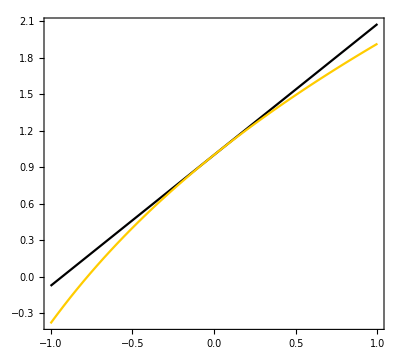

```mathematica
Plot[{Coeff1fσ8,Rate}/.Ωm0->0.3//Evaluate,{J̃,-1,1},Frame->True,Axes->False,AspectRatio->0.9,PlotRange->All,
PlotStyle->
{Directive[Black],Directive[RGBColor[1,0.8,0]]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\tilde{J}","\\frac{f \\sigma_8}{\\sigma_8}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->15}]
```

This is a verification that the J̃<<0 approximation is valid

### Growth Rate: Numerical Solution

```mathematica
δm[a_]=.
```

```mathematica
H0=1;
Ωm0=0.3;
ΩΛ=0.7;
ai=10^-3;
δi=1;
σ80=0.8;
```

```mathematica
Hub[a_]:=H0 √(Ωm0 a^-3+ΩΛ);
Geff[a_]=Simplify[-(2 ((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2))/(B6 ((-A6^2+2 A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2))/.ah[]->a/.HDESφ/.HDESI//.HDESII/.n->2/.ah[]->a,Assumptions->Ωm0>0&&a>0&&H0>0&&n>0];
```

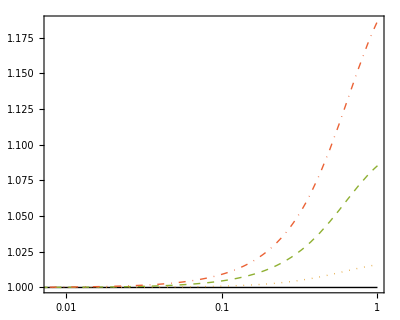

```mathematica
LogLinearPlot[{1,Geff[a]/.J->10^-2,Geff[a]/.J->5*10^-2,Geff[a]/.J->10^-1}//Evaluate,{a,ai,1},PlotRange->{{8*10^-3,1},Full},AspectRatio->0.8,Frame->True,PlotStyle->{Directive[Black,Thick],Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\frac{G_\\text{eff}}{G_N}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\Lambda \\text{CDM}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.01"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.05"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.1"]},
LegendLayout->{"Row",5},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.26,0.68}]]
```

In this case, HDES has a stronger gravity than ΛCDM

Numerical solution of the equation for δm

```mathematica
NSolδmΛ=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2 Ωm0/(a^5 Hub[a]^2)δm[a]==0,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES1=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->10^-2,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES2=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->5*10^-2,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES3=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->10^-1,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
```

This is a compilation of data for fσ8. You can find it in Sagredo, Nesseris, and Sapone 1806.10822 [astro-ph.CO].

```mathematica
datagrowth=Import["/Users/cosmologygroup/Desktop/PhD_Project/Theoretical_Work/ST_Theory/data_growth_2018_main.txt","Data"];
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

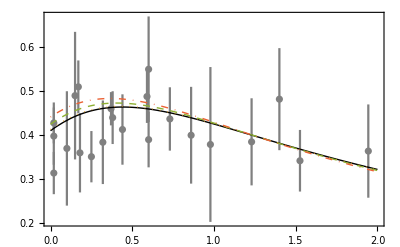

```mathematica
Show[ErrorListPlot[datagrowth,PlotStyle->Gray,PlotRange->All],Plot[{σ80 a δm'[a]/δm[1]/.NSolδmΛ,σ80 a δm'[a]/δm[1]/.NSolδmHDES1,σ80 a δm'[a]/δm[1]/.NSolδmHDES2,σ80 a δm'[a]/δm[1]/.NSolδmHDES3}/.a->1/(1+z)//Evaluate,{z,0,2},PlotStyle->{Directive[Black,Thick],Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed]},Frame->True,PlotRange->All],PlotRange->{{0,2},All},Frame->True,Axes->False,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"z","f\\sigma_8"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
H0=.;Ωm0=.;ΩΛ=.;ai=.;δi=.;σ80=.;
```

## Effective Fluid

### Density, Pressure, Velocity, and Sound Speed

These are the ℱ̂ coefficients in 1904.06294 [astro-ph.CO]. The following expressions were computed in “EFA_Horndeski.nb”

```mathematica
𝒩2=FullSimplify[-B9 D9 κ+3 A6 κ νφ-18 D9 (H^)^2-12 D9 Ḣ/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩3=FullSimplify[B9 mφ2 κ+18 mφ2 (H^)^2+12 mφ2 Ḣ/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩5=FullSimplify[A6^2 κ-B6 D9 κ/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩6=FullSimplify[B6 mφ2 κ/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩7=FullSimplify[2 D9-A6^2 κ+B6 D9 κ/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩8=FullSimplify[-2 mφ2+A4 D9 κ-B6 mφ2 κ+A6 κ μφ+6 D9 (H^)^2/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩9=FullSimplify[-A4 mφ2 κ-6 mφ2 (H^)^2/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩10=FullSimplify[A6 C4 κ-C3 D9 κ-2 D9 H^/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
𝒩11=FullSimplify[C3 mφ2 κ+2 mφ2 H^/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
```

```mathematica
SNSHδρDE=Simplify[-(k^4/((a^)^4)*𝒩7+k^2/((a^)^2)*𝒩8+𝒩9)/(k^4/((a^)^4)*𝒩5+k^2/((a^)^2)*𝒩6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

(4 a^(-1+(3 n)/4) J (Ω_m0+a^3 Ω_Λ) (4 a k^2 n+3 H_0^2 (-4+4 n+3 n^2) Ω_m0+12 a^3 H_0^2 (2+n) Ω_Λ))/(k^2 n (16 a^(3 n/4) J Ω_m0+16 a^(3+(3 n)/4) J Ω_Λ-3 √2 H_0 n (-2+3 n) Ω_m0^2 (Ω_m0+a^3 Ω_Λ)^(n/4)-12 √2 a^3 H_0 n Ω_m0 Ω_Λ (Ω_m0+a^3 Ω_Λ)^(n/4)))

0

```mathematica
SNSHδpDE=Simplify[1/3(k^2/((a^)^2)*𝒩2+𝒩3)/(k^4/((a^)^4)*𝒩5+k^2/((a^)^2)*𝒩6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

(3 a^(-1+(3 n)/4) H_0^2 J ((2+n) Ω_m0+4 a^3 Ω_Λ) ((-2+3 n) Ω_m0+4 a^3 Ω_Λ))/(k^2 (16 a^(3 n/4) J (Ω_m0+a^3 Ω_Λ)-3 √2 H_0 n Ω_m0 (Ω_m0+a^3 Ω_Λ)^(n/4) ((-2+3 n) Ω_m0+4 a^3 Ω_Λ)))

0

```mathematica
SNSHVDE=k^2/a*Simplify[(k^2/((a^)^2)*𝒩10+𝒩11)/(k^4/((a^)^4)*𝒩5+k^2/((a^)^2)*𝒩6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

-(8 a^(1+(3 n)/4) H_0 J (Ω_m0 √(Ω_m0/a^3+Ω_Λ)-2 Ω_Λ √(a^3 (Ω_m0+a^3 Ω_Λ))))/(16 a^(3 n/4) J Ω_m0+16 a^(3+(3 n)/4) J Ω_Λ-3 √2 H_0 n (-2+3 n) Ω_m0^2 (Ω_m0+a^3 Ω_Λ)^(n/4)-12 √2 a^3 H_0 n Ω_m0 Ω_Λ (Ω_m0+a^3 Ω_Λ)^(n/4))

0

Note that when J=0, all the perturbations goes to zero as expected

```mathematica
SNSHVDE/.n->1;
Series[%,{J,0,1}]//Normal;
Simplify[Series[%,{a,0,1}]//Normal,Assumptions->a>0]
```

(4 √2 a^(1/4) J)/(3 Ω_m0^(3/4))

This would be Eq. (187) from 1904.06294 [astro-ph.CO]

```mathematica
cs2DE=SNSHδpDE/SNSHδρDE//Simplify
```

(3 H_0^2 n ((2+n) Ω_m0+4 a^3 Ω_Λ) ((-2+3 n) Ω_m0+4 a^3 Ω_Λ))/(4 (Ω_m0+a^3 Ω_Λ) (4 a k^2 n+3 H_0^2 (-4+4 n+3 n^2) Ω_m0+12 a^3 H_0^2 (2+n) Ω_Λ))

This is the sound speed. Note that it does not depend on J.

```mathematica
H0=1;Subscript[Ω, Λ]=0.7;Subscript[Ω, m0]=0.3;k=300H0;
```

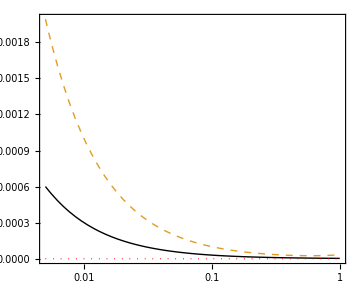

```mathematica
LogLinearPlot[{3*10^-6 a^-1,cs2DE/.n->2,0}//Evaluate,{a,5*10^-3,1},Frame->True,Axes->False,AspectRatio->0.8,PlotRange->All,
PlotStyle->
{Directive[Thick,Black],Directive[Thick,Dashed],Directive[Thick,Dotted,Red]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{SH Bound}"]},
LegendLayout->{"Row",5},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.75,0.84}]]
```

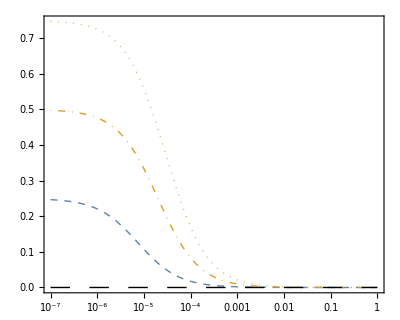

```mathematica
LogLinearPlot[{cs2DE/.n->1,cs2DE/.n->2,cs2DE/.n->3,0}//Evaluate,{a,10^-7,1},Frame->True,Axes->False,AspectRatio->0.8,PlotRange->All,
PlotStyle->
{Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dotted],Directive[Black,Thick,Dashing[Large]]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["n = 1"],(MaTeX[#,Magnification->1.4]&)/@Style["n = 2"],(MaTeX[#,Magnification->1.4]&)/@Style["n = 3"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.79,0.75}]]
```

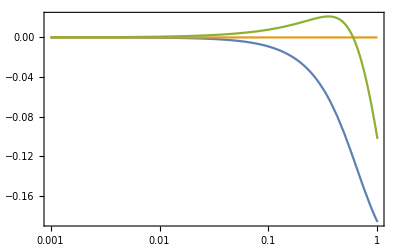

```mathematica
Plot[{SNSHδρDE,SNSHδpDE,SNSHVDE}/.n->2/.J->10^-1//Evaluate,{a,10^-3,1},Frame->True,PlotRange->All,ScalingFunctions->{"Log"},
PlotStyle->
{Directive[Thick],Directive[Thick],Directive[Thick]},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta \\rho_\\text{DE} / \\delta \\rho_m","\\delta p_\\text{DE} / \\delta \\rho_m","\\rho_\\text{DE} V_\\text{DE} / \\delta \\rho_m"},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
{SNSHδρDE,SNSHδpDE,SNSHVDE}/.a->10^-3/.n->2/.J->5*10^-2
```

{-4.62683×10^-6,-4.53611×10^-8,0.0000392839}

```mathematica
Subscript[H, 0]=.;Subscript[Ω, Λ]=.;Subscript[Ω, m0]=.;k=.;
```

### Evolution of Perturbations

```mathematica
δ0=1; (* Overall Scale *)
H0=1; (* km s^-1 Mpc^-1 *)
Ωm0=0.3; (* Matter Today *)
ΩΛ=0.7; (* Dark Energy Today *)
k=300; (* Momentum *)
wDE=-1;(* Equation of State *)
```

Initial conditions:

```mathematica
ai=10^-3;
δmi=δ0*ai(1+3*(Hub[ai]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φi=-3/2 δ0*H0^2*Ωm0/k^2;
ρDEN=ρDE/.HDESφ/.HDESI//.HDESII/.ah[]->a;
```

Functions

```mathematica
Hub[a_]=H0 √(Ωm0*a^-3+ΩΛ); 
Φ[a_]=-3/2 H0^2/(a*k^2)(Ωm0(δm[a]+(3a*Hub[a])/k^2*Vm[a])+ΩΛ*a^(-3wDE)(δDEA[a]+(3a*Hub[a])/k^2*VDEA[a])); 
δDEA[a_]=SNSHδρDE(Ωm0*a^-3)/(ρDEN/(3 H0^2))*δm[a];
VDEA[a_]=SNSHVDE(Ωm0*a^-3)/(ρDEN/(3 H0^2))*δm[a];
```

Evolution Equations Matter

```mathematica
Eqδm[a_]=-δm'[a]-Vm[a]/(a^2*Hub[a])+3Φ'[a];
EqVm[a_]=-Vm'[a]-Vm[a]/a+k^2/(a^2*Hub[a])Φ[a];
```

```mathematica
SolPertsI=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.n->2/.J->5*10^-2,{δm,Vm},{a,ai,1}][[1]]
```

{δm→InterpolatingFunction[…],Vm→InterpolatingFunction[…]}

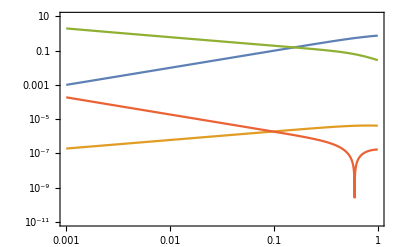

```mathematica
LogLogPlot[{{δm[a],Vm[a]/k^2,δDEA[a],VDEA[a]/k^2}/.n->2/.J->5*10^-2/.SolPertsI}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-11,10},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta_m","\\frac{V_m}{k^2}","\\delta_\\text{DE}","\\frac{V_\\text{DE}}{k^2}"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

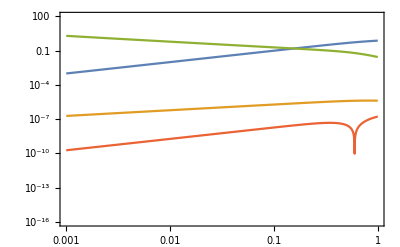

```mathematica
LogLogPlot[{{δm[a],Vm[a]/k^2,δDEA[a],a^2/k^2 VDEA[a]}/.n->2/.J->5*10^-2/.SolPertsI}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-16,100},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta_m","\\frac{V_m}{k^2}","\\delta_\\text{DE}","\\frac{a^2}{k^2} V_\\text{DE}"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
{δm[ai],Vm[ai]/k^2,δDEA[ai],VDEA[ai]/k^2}/.n->2/.J->5*10^-2/.SolPertsI
```

{0.00101,-1.9245×10^-7,-2.00276,0.000188937}

```mathematica
δ0=.;H0=.;Ωm0=.;ΩΛ=.;k=.;wDE=.;
```

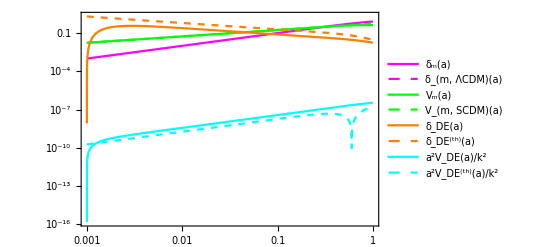

```mathematica
(**************)
```

This is the plot in the notebook in

```mathematica
Hyperlink["https://members.ift.uam-csic.es/savvas.nesseris/efclass.html"]
```

https://members.ift.uam-csic.es/savvas.nesseris/efclass.html

The results agree with those in 1904.06294 [astro-ph.CO]. Now, we apply our approach.

## Perturbations (Dropping H)

## Perturbation Coefficients

We neglect H from the beginning

```mathematica
A1=Simplify[-12 Subscript[G, 4] H^-6 Subscript[G, 4  φ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A2=Simplify[6 Subscript[G, 4  φ] H^-Subscript[G, 2 Subscript[X, 1]] φ̇+2 Subscript[G, 3  φ] φ̇-9 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3+Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A3=Simplify[-4 Subscript[G, 4]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A4=Simplify[-12 Subscript[G, 4] (H^)^2-12 Subscript[G, 4  φ] H^ φ̇+Subscript[G, 2 Subscript[X, 1]] (φ̇)^2-2 Subscript[G, 3  φ] (φ̇)^2+12 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^4-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^4+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^5/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
A6=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
μφ=Simplify[-Subscript[G, 2  φ]-6 Subscript[G, 4  φ] (H^)^2-6 Subscript[G, 4  φφ] H^ φ̇+Subscript[G, 2 Subscript[φX, 1]] (φ̇)^2-Subscript[G, 3  φφ] (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^3/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

C1=Simplify[-4 Subscript[G, 4]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C2=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C3=Simplify[-4 Subscript[G, 4] H^-2 Subscript[G, 4  φ] φ̇+Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
C4=Simplify[-2 Subscript[G, 4  φ] H^+Subscript[G, 2 Subscript[X, 1]] φ̇-2 Subscript[G, 3  φ] φ̇+2 Subscript[G, 4  φφ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

B1=Simplify[-12 Subscript[G, 4]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B2=Simplify[6 Subscript[G, 4  φ]-3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B3=Simplify[-36 Subscript[G, 4] H^-12 Subscript[G, 4  φ] φ̇/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B4=Simplify[12 Subscript[G, 4  φ] H^+3 Subscript[G, 2 Subscript[X, 1]] φ̇-6 Subscript[G, 3  φ] φ̇+12 Subscript[G, 4  φφ] φ̇-3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3-6 Subscript[G, 3 Subscript[X, 1]] φ̇ φ^(..)-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B5=Simplify[-12 Subscript[G, 4] H^-6 Subscript[G, 4  φ] φ̇+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^3/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B6=Simplify[-4 Subscript[G, 4]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B7=Simplify[4 Subscript[G, 4  φ]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B8=Simplify[4 Subscript[G, 4]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B9=Simplify[-36 Subscript[G, 4] (H^)^2-24 Subscript[G, 4] Ḣ-24 Subscript[G, 4  φ] H^ φ̇-3 Subscript[G, 2 Subscript[X, 1]] (φ̇)^2+6 Subscript[G, 3  φ] (φ̇)^2-12 Subscript[G, 4  φφ] (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^4-12 Subscript[G, 4  φ] φ^(..)+12 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2 φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
B0=Simplify[-6 Subscript[G, 2]-36 Subscript[G, 4] (H^)^2-24 Subscript[G, 4] Ḣ-24 Subscript[G, 4  φ] H^ φ̇+6 Subscript[G, 3  φ] (φ̇)^2-12 Subscript[G, 4  φφ] (φ̇)^2-12 Subscript[G, 4  φ] φ^(..)+6 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
νφ=Simplify[Subscript[G, 2  φ]+6 Subscript[G, 4  φ] (H^)^2+4 Subscript[G, 4  φ] Ḣ+4 Subscript[G, 4  φφ] H^ φ̇-Subscript[G, 3  φφ] (φ̇)^2+2 Subscript[G, 4  φφφ] (φ̇)^2+2 Subscript[G, 4  φφ] φ^(..)-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];

D1=Simplify[-6 Subscript[G, 4  φ]+3 Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D2=Simplify[-Subscript[G, 2 Subscript[X, 1]]+2 Subscript[G, 3  φ]-6 Subscript[G, 3 Subscript[X, 1]] H^ φ̇-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2+Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D3=Simplify[-24 Subscript[G, 4  φ] H^+3 Subscript[G, 2 Subscript[X, 1]] φ̇-6 Subscript[G, 3  φ] φ̇+18 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3+6 Subscript[G, 3 Subscript[X, 1]] φ̇ φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D4=Simplify[-3 Subscript[G, 2 Subscript[X, 1]] H^+6 Subscript[G, 3  φ] H^-Subscript[G, 2 Subscript[φX, 1]] φ̇+2 Subscript[G, 3  φφ] φ̇-18 Subscript[G, 3 Subscript[X, 1]] (H^)^2 φ̇-6 Subscript[G, 3 Subscript[X, 1]] Ḣ φ̇-3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^2-3 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^2-Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^3+Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^3-9 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (H^)^2 (φ̇)^3-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] Ḣ (φ̇)^3-3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^4-6 Subscript[G, 3 Subscript[X, 1]] H^ φ^(..)-3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] φ̇ φ^(..)+4 Subscript[G, 3 Subscript[φX, 1]] φ̇ φ^(..)-15 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^2 φ^(..)-Subscript[G, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)+Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^3 φ^(..)-3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D5=Simplify[-6 Subscript[G, 4  φ] H^+Subscript[G, 2 Subscript[X, 1]] φ̇-2 Subscript[G, 3  φ] φ̇+9 Subscript[G, 3 Subscript[X, 1]] H^ (φ̇)^2+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^3-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^3+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^4/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D7=Simplify[-4 Subscript[G, 4  φ]/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D8=Simplify[0/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D9=Simplify[-Subscript[G, 2 Subscript[X, 1]]+2 Subscript[G, 3  φ]-4 Subscript[G, 3 Subscript[X, 1]] H^ φ̇-Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2-2 Subscript[G, 3 Subscript[X, 1]] φ^(..)-Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D10=Simplify[2 Subscript[G, 4  φ]-Subscript[G, 3 Subscript[X, 1]] (φ̇)^2/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
D11=Simplify[-24 Subscript[G, 4  φ] (H^)^2-12 Subscript[G, 4  φ] Ḣ+6 Subscript[G, 2 Subscript[X, 1]] H^ φ̇-12 Subscript[G, 3  φ] H^ φ̇+Subscript[G, 2 Subscript[φX, 1]] (φ̇)^2-2 Subscript[G, 3  φφ] (φ̇)^2+36 Subscript[G, 3 Subscript[X, 1]] (H^)^2 (φ̇)^2+12 Subscript[G, 3 Subscript[X, 1]] Ḣ (φ̇)^2+3 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3+6 Subscript[G, 3 Subscript[φX, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^4-Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^4+9 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] (H^)^2 (φ̇)^4+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] Ḣ (φ̇)^4+3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^5+2 Subscript[G, 2 Subscript[X, 1]] φ^(..)-4 Subscript[G, 3  φ] φ^(..)+24 Subscript[G, 3 Subscript[X, 1]] H^ φ̇ φ^(..)+5 Subscript[G, 2 Subscript[X, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)-6 Subscript[G, 3 Subscript[φX, 1]] (φ̇)^2 φ^(..)+24 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^3 φ^(..)+Subscript[G, 2 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)-Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^4 φ^(..)+3 Subscript[G, 3 Subscript[X, 1] Subscript[X, 1] Subscript[X, 1]] H^ (φ̇)^5 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
mφ2=Simplify[-Subscript[G, 2  φφ]-12 Subscript[G, 4  φφ] (H^)^2-6 Subscript[G, 4  φφ] Ḣ+3 Subscript[G, 2 Subscript[φX, 1]] H^ φ̇-6 Subscript[G, 3  φφ] H^ φ̇+Subscript[G, 2 Subscript[φφX, 1]] (φ̇)^2-Subscript[G, 3  φφφ] (φ̇)^2+9 Subscript[G, 3 Subscript[φX, 1]] (H^)^2 (φ̇)^2+3 Subscript[G, 3 Subscript[φX, 1]] Ḣ (φ̇)^2+3 Subscript[G, 3 Subscript[φφX, 1]] H^ (φ̇)^3+Subscript[G, 2 Subscript[φX, 1]] φ^(..)-2 Subscript[G, 3  φφ] φ^(..)+6 Subscript[G, 3 Subscript[φX, 1]] H^ φ̇ φ^(..)+Subscript[G, 2 Subscript[φX, 1] Subscript[X, 1]] (φ̇)^2 φ^(..)-Subscript[G, 3 Subscript[φφX, 1]] (φ̇)^2 φ^(..)+3 Subscript[G, 3 Subscript[φX, 1] Subscript[X, 1]] H^ (φ̇)^3 φ^(..)/.H^->0/.Ḣ->0/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&ah[]>0&&H0>0&&n>0];
```

Gravitational Slip Parameters

```mathematica
η=((A6-B7) B7 k^2)/((A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2)/.ah[]->a/.HDESφ/.HDESI//.HDESII
```

0

```mathematica
γ=((A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2)/((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2)/.ah[]->a/.HDESφ/.HDESI//.HDESII//Simplify
```

1

## Potential and Matter Domination

### G_eff

```mathematica
Subscript[G, eff]/G->Simplify[-(2 ((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2))/(B6 ((-A6^2+2 A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2))/.ah[]->a/.HDESφ/.HDESI//.HDESII/.ΩΛ->0/.n->2/.ah[]->a,Assumptions->Ωm0>0&&a>0&&H0>0&&n>0]
```

G_eff/G→(9 √2 H_0 (Ω_m0/a)^(3/2))/(2 J+9 √2 H_0 (Ω_m0/a)^(3/2))

```mathematica
Simplify[Series[(9 √2 Subscript[H, 0] (Subscript[Ω, m0]/a)^(3/2))/(2 J+9 √2 Subscript[H, 0] (Subscript[Ω, m0]/a)^(3/2)),{J,0,1}]//Normal,Assumptions->a>0]/.J->H0*J̃
```

1-(√2 a^(3/2) J̃)/(9 Ω_m0^(3/2))

Note that this differs from Eq. (177) in 1904.06294 [astro-ph.CO]

```mathematica
D[H0*Ωm0^(1/2)*a^(-3/2),a]/(H0*Ωm0^(1/2)*a^(-3/2))//Simplify
```

-3/(2 a)

```mathematica
Solδm=DSolve[δm''[a]+(3/a-3/(2 a))δm'[a]-3/(2 a^2)(1-(√2 a^(3/2) J̃)/(9 Subscript[Ω, m0]^(3/2)))δm[a]==0//Expand,δm[a],a][[1]]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{δm[a]→(√3 Ω_m0^(1/4) BesselJ[-5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 √3 Ω_m0^(3/4))] C[1] Gamma[-2/3])/(2^(1/4) a^(1/4) (J̃)^(1/6))+(√3 Ω_m0^(1/4) BesselJ[5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 √3 Ω_m0^(3/4))] C[2] Gamma[8/3])/(2^(1/4) a^(1/4) (J̃)^(1/6))}

Determination of the constants C[2] . The first term in δm[a] is the decaying mode.

Expand δm  around  a=0

```mathematica
Ss=Simplify[Series[Solδm[[1,2]]/.C[1]->0,{a,0,3}],Assumptions->Ωm0>0&&H0>0&&a>0&&J>0]
```

(2 C[2] (J̃)^(2/3) a)/(9 Ω_m0)-((C[2] (J̃)^(5/3)) a^(5/2))/(81 (√2 Ω_m0^(5/2)))+O[a]^4

During matter domination δm[a]∝a

```mathematica
Solc2=Simplify[Solve[SeriesCoefficient[Ss,1]==1, C[2]][[1]],Assumptions->Ωm0>0&&H0>0&&a>0&&J>0]
```

{C[2]→(9 Ω_m0)/(2 (J̃)^(2/3))}

```mathematica
δm[a_]=Solδm[[1,2]]/.C[1]->0/.Solc2//Simplify
```

(9 √3 Ω_m0^(5/4) BesselJ[5/3,(2 2^(3/4) a^(3/4) √(J̃))/(3 √3 Ω_m0^(3/4))] Gamma[8/3])/(2 2^(1/4) a^(1/4) (J̃)^(5/6))

### Growth Rate: Analytical Solution

```mathematica
fσ8=σ8 a D[δm[a],a]/δm[1]//FullSimplify
```

(3 √a σ8 (Hypergeometric0F1Regularized[5/3,-(2 √2 a^(3/2) J̃)/(27 Ω_m0^(3/2))]-Hypergeometric0F1Regularized[8/3,-(2 √2 a^(3/2) J̃)/(27 Ω_m0^(3/2))]) ((a^(3/4) √(J̃))/Ω_m0^(3/4))^(2/3))/(2 Hypergeometric0F1Regularized[8/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))] ((√(J̃))/Ω_m0^(3/4))^(2/3))

Expansion around today: a=1

```mathematica
Seriesfσ8=Series[fσ8,{a,1,1}]//FullSimplify
```

3/2 σ8 (-1+Hypergeometric0F1Regularized[5/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))]/Hypergeometric0F1Regularized[8/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))])+1/12 σ8 (27-(9 Hypergeometric0F1Regularized[5/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))])/Hypergeometric0F1Regularized[8/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))]-(2 √2 J̃)/Ω_m0^(3/2)) (a-1)+O[a-1]^2

```mathematica
Simfσ8=Seriesfσ8/σ8/.Hypergeometric0F1Regularized[5/3,-(2 √2 J̃)/(27 Subscript[Ω, m0]^(3/2))]->α1/.Hypergeometric0F1Regularized[8/3,-(2 √2 J̃)/(27 Subscript[Ω, m0]^(3/2))]->α2
```

3/2 (-1+α1/α2)+1/12 (27-(9 α1)/α2-(2 √2 J̃)/Ω_m0^(3/2)) (a-1)+O[a-1]^2

Expansion of  fσ8 around J̃=0  for a=1→ We only need the first coefficient

```mathematica
Coeff1fσ8=Series[SeriesCoefficient[Seriesfσ8,0]/σ8,{J̃,0,1}]//Normal
```

3/2 (-1+Gamma[8/3]/Gamma[5/3])-(√2 (-Gamma[8/3]^2+Gamma[5/3] Gamma[11/3]) J̃)/(9 Ω_m0^(3/2) Gamma[5/3] Gamma[11/3])

```mathematica
Rate=Seriesfσ8/σ8/.a->1//FullSimplify//Factor//FullSimplify
```

3/2 (-1+Hypergeometric0F1Regularized[5/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))]/Hypergeometric0F1Regularized[8/3,-(2 √2 J̃)/(27 Ω_m0^(3/2))])

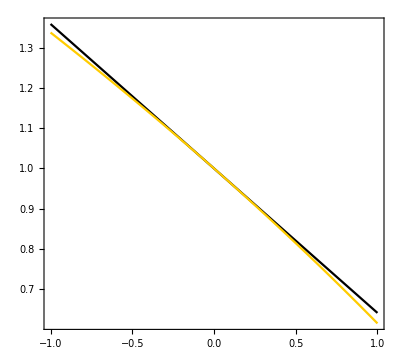

```mathematica
Plot[{Coeff1fσ8,Rate}/.Ωm0->0.3//Evaluate,{J̃,-1,1},Frame->True,Axes->False,AspectRatio->0.9,PlotRange->All,
PlotStyle->
{Directive[Black],Directive[RGBColor[1,0.8,0]]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\tilde{J}","\\frac{f \\sigma_8}{\\sigma_8}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->15}]
```

This is a verification that the J̃<<0 approximation is valid. We see that in this case fσ8 decays with J̃, even the approximation extend to greater J̃ (valid until J̃∼0.5)

### Growth Rate: Numerical Solution

```mathematica
δm[a_]=.
```

```mathematica
H0=1;
Ωm0=0.3;
ΩΛ=0.7;
ai=10^-3;
δi=1;
σ80=0.8;
```

```mathematica
Hub[a_]:=H0 √(Ωm0 a^-3+ΩΛ);
Geff[a_]=Simplify[-(2 ((B7^2+B6 D9) k^2-B6 mφ2 (a^)^2))/(B6 ((-A6^2+2 A6 B7+B6 D9) k^2-B6 mφ2 (a^)^2))/.ah[]->a/.HDESφ/.HDESI//.HDESII/.n->2/.ah[]->a,Assumptions->Ωm0>0&&a>0&&H0>0&&n>0];
```

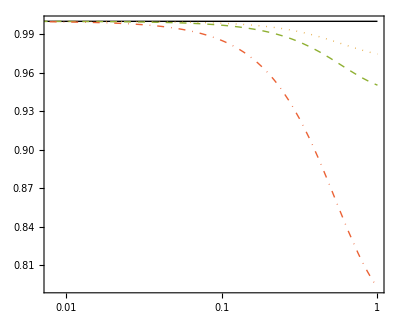

```mathematica
LogLinearPlot[{1,Geff[a]/.J->5*10^-2,Geff[a]/.J->10^-1,Geff[a]/.J->0.5}//Evaluate,{a,ai,1},PlotRange->{{8*10^-3,1},Full},AspectRatio->0.8,Frame->True,PlotStyle->{Directive[Black,Thick],Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\frac{G_\\text{eff}}{G_N}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\Lambda \\text{CDM}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.05"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.1"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\tilde{J} = 0.5"]},
LegendLayout->{"Row",5},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.26,0.32}]]
```

In this case gravity is weaker than in the standard model.

```mathematica
NSolδmΛ=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2 Ωm0/(a^5 Hub[a]^2)δm[a]==0,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES1=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->5*10^-2,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES2=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->10^-1,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
NSolδmHDES3=NDSolve[{δm''[a]+(3/a+Hub'[a]/Hub[a])δm'[a]-3/2(Ωm0 Geff[a])/(a^5 Hub[a]^2)δm[a]==0/.J->0.5,δm[ai]==δi*ai,δm'[ai]==δi},δm,{a,ai,1}][[1]];
```

This is a compilation of data for fσ8. You can find it in Sagredo, Nesseris, and Sapone 1806.10822 [astro-ph.CO].

```mathematica
datagrowth=Import["/Users/cosmologygroup/Desktop/PhD_Project/Theoretical_Work/ST_Theory/data_growth_2018_main.txt","Data"];
Needs["ErrorBarPlots`"];
```

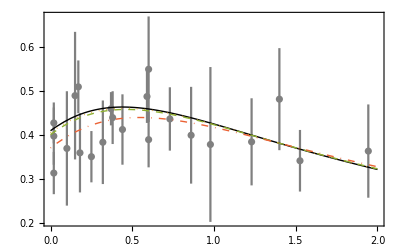

```mathematica
Show[ErrorListPlot[datagrowth,PlotStyle->Gray,PlotRange->All],Plot[{σ80 a δm'[a]/δm[1]/.NSolδmΛ,σ80 a δm'[a]/δm[1]/.NSolδmHDES1,σ80 a δm'[a]/δm[1]/.NSolδmHDES2,σ80 a δm'[a]/δm[1]/.NSolδmHDES3}/.a->1/(1+z)//Evaluate,{z,0,2},PlotStyle->{Directive[Black,Thick],Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed]},Frame->True,PlotRange->All],PlotRange->{{0,2},All},Frame->True,Axes->False,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"z","f\\sigma_8"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
H0=.;Ωm0=.;ΩΛ=.;ai=.;δi=.;σ80=.;
```

## Effective Fluid

### Density, Pressure, Velocity, and Sound Speed

These are the ℱ̂ coefficients in 1904.06294 [astro-ph.CO] neglecting H

```mathematica
ℳ2=FullSimplify[-B9 D9+3 A6 νφ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ3=FullSimplify[B9 mφ2/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ5=FullSimplify[A6^2 κ-B6 D9 κ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ6=FullSimplify[B6 mφ2 κ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ7=FullSimplify[2 D9-A6^2 κ+B6 D9 κ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ8=FullSimplify[-2 mφ2+A4 D9 κ-B6 mφ2 κ+A6 κ μφ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ9=FullSimplify[-A4 mφ2 κ/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ10=FullSimplify[A6 C4-C3 D9/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
ℳ11=FullSimplify[C3 mφ2/.H^->0/.Ḣ->0/.ah[]->a/.HDESφ/.HDESI//.HDESII,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0&&n>0];
```

```mathematica
SNSδρDE=Simplify[(k^4/((a^)^4)*ℳ7+k^2/((a^)^2)*ℳ8+ℳ9)/(k^4/((a^)^4)*ℳ5+k^2/((a^)^2)*ℳ6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

(4 a^(-1+(3 n)/4) J (Ω_m0+a^3 Ω_Λ) (-4 a k^2 n+9 H_0^2 (24-10 n+n^2) Ω_m0-36 a^3 H_0^2 (-4+n) Ω_Λ))/(k^2 n (16 a^(3 n/4) J Ω_m0+16 a^(3+(3 n)/4) J Ω_Λ-9 √2 H_0 (-6+n) n Ω_m0^2 (Ω_m0+a^3 Ω_Λ)^(n/4)+36 √2 a^3 H_0 n Ω_m0 Ω_Λ (Ω_m0+a^3 Ω_Λ)^(n/4)))

0

```mathematica
SNSδpDE=Simplify[1/3(k^2/((a^)^2)*ℳ2+ℳ3)/(k^4/((a^)^4)*ℳ5+k^2/((a^)^2)*ℳ6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

(9 a^(-1+(3 n)/4) H_0^2 J ((-6+n) Ω_m0-4 a^3 Ω_Λ) ((2+n) Ω_m0+4 a^3 Ω_Λ))/(k^2 (16 a^(3 n/4) J (Ω_m0+a^3 Ω_Λ)-9 √2 H_0 n Ω_m0 ((-6+n) Ω_m0-4 a^3 Ω_Λ) (Ω_m0+a^3 Ω_Λ)^(n/4)))

0

```mathematica
SNSVDE=k^2/a*Simplify[(k^2/((a^)^2)*ℳ10+ℳ11)/(k^4/((a^)^4)*ℳ5+k^2/((a^)^2)*ℳ6)*δρm/.ah[]->a/.δρm->1,Assumptions->Ωm0>0&&ΩΛ>0&&a>0&&H0>0]
%/.J->0//Simplify
```

-(24 a^(-1+(3 n)/4) H_0 J Ω_m0 √(a (Ω_m0+a^3 Ω_Λ)))/(16 a^(3 n/4) J (Ω_m0+a^3 Ω_Λ)-9 √2 H_0 n Ω_m0 ((-6+n) Ω_m0-4 a^3 Ω_Λ) (Ω_m0+a^3 Ω_Λ)^(n/4))

0

```mathematica
SNSVDE/.n->1;
Series[%,{J,0,1}]//Normal;
Simplify[Series[%,{a,0,1}]//Normal,Assumptions->a>0]
%/.J->0
```

-(4 √2 a^(1/4) J)/(15 Ω_m0^(3/4))

0

This is also not Eq. (187) from 1904.06294 [astro-ph.CO]

```mathematica
cs2DE=SNSδpDE/SNSδρDE//Simplify
```

(9 H_0^2 n ((-6+n) Ω_m0-4 a^3 Ω_Λ) ((2+n) Ω_m0+4 a^3 Ω_Λ))/(4 (Ω_m0+a^3 Ω_Λ) (-4 a k^2 n+9 H_0^2 (24-10 n+n^2) Ω_m0-36 a^3 H_0^2 (-4+n) Ω_Λ))

This is the sound speed. Note that it does not depend on J.

```mathematica
H0=1;Subscript[Ω, Λ]=0.7;Subscript[Ω, m0]=0.3;k=300H0;
```

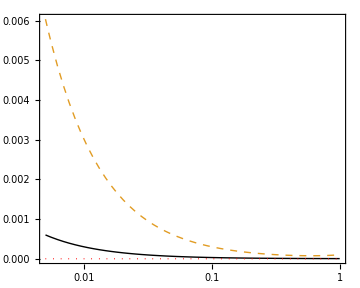

```mathematica
LogLinearPlot[{3*10^-6 a^-1,cs2DE/.n->2,0}//Evaluate,{a,5*10^-3,1},Frame->True,Axes->False,AspectRatio->0.8,PlotRange->All,
PlotStyle->
{Directive[Thick,Black],Directive[Thick,Dashed],Directive[Thick,Dotted,Red]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{SH Bound}"]},
LegendLayout->{"Row",5},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.75,0.84}]]
```

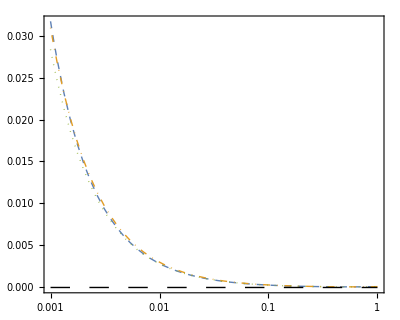

```mathematica
LogLinearPlot[{cs2DE/.n->1,cs2DE/.n->2,cs2DE/.n->3,0}//Evaluate,{a,10^-3,1},Frame->True,Axes->False,AspectRatio->0.8,PlotRange->All,
PlotStyle->
{Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dotted],Directive[Black,Thick,Dashing[Large]]},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","c_{s, \\text{DE}}^2"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["n = 1"],(MaTeX[#,Magnification->1.4]&)/@Style["n = 2"],(MaTeX[#,Magnification->1.4]&)/@Style["n = 3"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.79,0.75}]]
```

In this case, the sound speed diverges for a<10^-4. This was expected the QSA is valid only during matter domination when the potential are constants. Specifically, some time after decoupling which occurs around a∼9×10^-4.

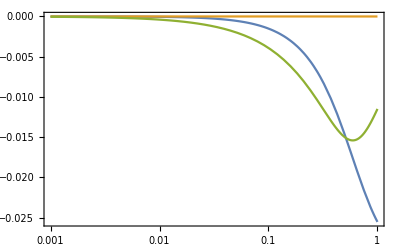

```mathematica
Plot[{SNSδρDE,SNSδpDE,SNSVDE}/.n->2/.J->5*10^-2//Evaluate,{a,10^-3,1},Frame->True,PlotRange->All,ScalingFunctions->{"Log"},
PlotStyle->
{Directive[Thick],Directive[Thick],Directive[Thick]},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta \\rho_\\text{DE} / \\delta \\rho_m","\\delta p_\\text{DE} / \\delta \\rho_m","\\rho_\\text{DE} V_\\text{DE} / \\delta \\rho_m"},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
{SNSδρDE,SNSδpDE,SNSVDE}/.a->10^-3/.n->2/.J->5*10^-2
```

{-1.46667×10^-6,-4.53609×10^-8,-0.0000392837}

```mathematica
Subscript[H, 0]=.;Subscript[Ω, Λ]=.;Subscript[Ω, m0]=.;k=.;
```

### Evolution of Perturbations

```mathematica
δ0=1; (* Overall Scale *)
H0=1; (* km s^-1 Mpc^-1 *)
Ωm0=0.3; (* Matter Today *)
ΩΛ=0.7; (* Dark Energy Today *)
k=300; (* Momentum *)
wDE=-1;(* Equation of State *)
```

Initial conditions:

```mathematica
ai=10^-3;
δmi=δ0*ai(1+3*(Hub[ai]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φi=-3/2 δ0*H0^2*Ωm0/k^2;
ρDEN=ρDE/.HDESφ/.HDESI//.HDESII/.ah[]->a;
```

Functions

```mathematica
Hub[a_]=H0 √(Ωm0*a^-3+ΩΛ); 
Φ[a_]=-3/2 H0^2/(a*k^2)(Ωm0(δm[a]+(3a*Hub[a])/k^2*Vm[a])+ΩΛ*a^(-3wDE)(δDEA[a]+(3a*Hub[a])/k^2*VDEA[a])); 
δDEA[a_]=SNSδρDE(Ωm0*a^-3)/(ρDEN/(3 H0^2))*δm[a];
VDEA[a_]=SNSVDE(Ωm0*a^-3)/(ρDEN/(3 H0^2))*δm[a];
```

Evolution Equations Matter

```mathematica
Eqδm[a_]=-δm'[a]-Vm[a]/(a^2*Hub[a])+3Φ'[a];
EqVm[a_]=-Vm'[a]-Vm[a]/a+k^2/(a^2*Hub[a])Φ[a];
```

```mathematica
SolPertsII=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.n->2/.J->5*10^-2,{δm,Vm},{a,ai,1}][[1]]
```

{δm→InterpolatingFunction[…],Vm→InterpolatingFunction[…]}

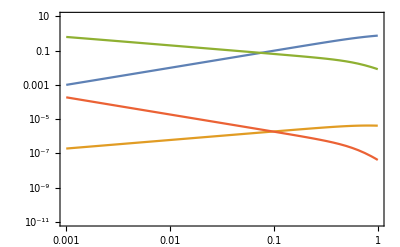

```mathematica
LogLogPlot[{{δm[a],Vm[a]/k^2,δDEA[a],VDEA[a]/k^2}/.n->2/.J->5*10^-2/.SolPertsII}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-11,10},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta_m","\\frac{V_m}{k^2}","\\delta_\\text{DE}","\\frac{V_\\text{DE}}{k^2}"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

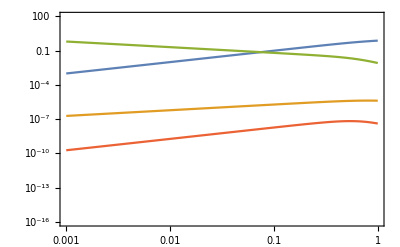

```mathematica
LogLogPlot[{{δm[a],Vm[a]/k^2,δDEA[a],a^2/k^2 VDEA[a]}/.n->2/.J->5*10^-2/.SolPertsII}//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->{10^-16,100},FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->18/12]&)/@{"\\delta_m","\\frac{V_m}{k^2}","\\delta_\\text{DE}","\\frac{a^2}{k^2} V_\\text{DE}"},BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
{δm[ai],Vm[ai]/k^2,δDEA[ai],VDEA[ai]/k^2}/.n->2/.J->5*10^-2/.SolPertsII
```

{0.00101,-1.9245×10^-7,-0.634858,-0.000188936}

In this case we do not see the peak in the velocity which was obtained with the approach keeping H(see below), but the behaviour is very similar.

-Graphics-

-Graphics-

```mathematica
δ0=.;H0=.;Ωm0=.;ΩΛ=.;k=.;wDE=.;
```

Note that our results are more similar to the results with solid lines {"δ_DE(a)","a^2V_DE(a)/k^2"}  in this plot, which was obtained solving the full perturbations.

-Graphics-

## CMB Angular and Matter Power Spectra

We confront the two approaches in HDES wrt observables as the matter power spectrum, and the CMB power spectra. The computations are performed using EFCLASS.

You should replace the location of your files here:

```mathematica
dataPkHDESW=Import["/Users/cosmologygroup/EFCLASS/output/HDESW00_pk.dat",{"Data",{All},{1,2}}];
dataPkHDESB=Import["/Users/cosmologygroup/EFCLASS/output/HDESB00_pk.dat",{"Data",{All},{1,2}}];
```

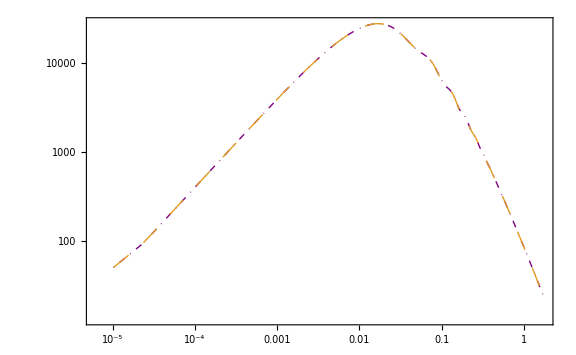

```mathematica
MatterSpectrum=ListLogLogPlot[{dataPkHDESW,dataPkHDESB},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\left[ h \\text{Mpc}^{-1} \\right]","P(k) \\left[ (h^{-1} \\text{Mpc})^3 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,DotDashed,Purple],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{HDESW}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\text{HDESB}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.6,0.20}],ImageSize->Large]
```

Here we only consider the first 50 multi-poles. The remaining multi-poles are erased from data and recovered after the plot is made.

```mathematica
dataClTTHDESW=Import["/Users/cosmologygroup/EFCLASS/output/HDESW00_cl50.dat",{"Data",{All},{1,2}}];
dataClTTHDESB=Import["/Users/cosmologygroup/EFCLASS/output/HDESB00_cl50.dat",{"Data",{All},{1,2}}];
dataClTTΛCDM=Import["/Users/cosmologygroup/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_cl50.dat",{"Data",{All},{1,2}}];
```

Import::noelem: The Import element "2" is not present when importing as Table.

This is necessary in order to get the right units.

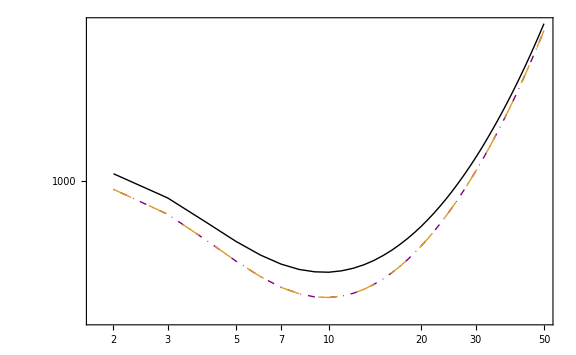

```mathematica
ClTTHDESB={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTHDESB;
ClTTHDESW={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTHDESW; 
ClTTΛCDM={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTΛCDM;
TTSpectrum=ListLogLogPlot[{ClTTHDESB,ClTTHDESB,ClTTΛCDM}//Evaluate,Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TT} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,DotDashed,Purple],Directive[Thick,Dashing[Large]],Directive[Thick,Black]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{HDESW}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\text{HDESB}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.5,0.75}],ImageSize->Large]
```

This is the plot in the left panel of Fig. 5 in 1904.06294 [astro-ph.CO]

All multi-poles computed by EFCLASS are considered here

```mathematica
dataClTTHDESW=Import["/Users/cosmologygroup/EFCLASS/output/HDESW00_cl.dat",{"Data",{All},{1,2}}];
dataClTTHDESB=Import["/Users/cosmologygroup/EFCLASS/output/HDESB00_cl.dat",{"Data",{All},{1,2}}];
```

Import::noelem: The Import element "2" is not present when importing as Table.

```mathematica
dataClEEHDESW=Import["/Users/cosmologygroup/EFCLASS/output/HDESW00_cl.dat",{"Data",{All},{1,3}}];
dataClEEHDESB=Import["/Users/cosmologygroup/EFCLASS/output/HDESB00_cl.dat",{"Data",{All},{1,3}}];
```

Import::noelem: The Import element "3" is not present when importing as Table.

```mathematica
dataClTEHDESW=Import["/Users/cosmologygroup/EFCLASS/output/HDESW00_cl.dat",{"Data",{All},{1,4}}];
dataClTEHDESB=Import["/Users/cosmologygroup/EFCLASS/output/HDESB00_cl.dat",{"Data",{All},{1,4}}];
```

Import::noelem: The Import element "4" is not present when importing as Table.

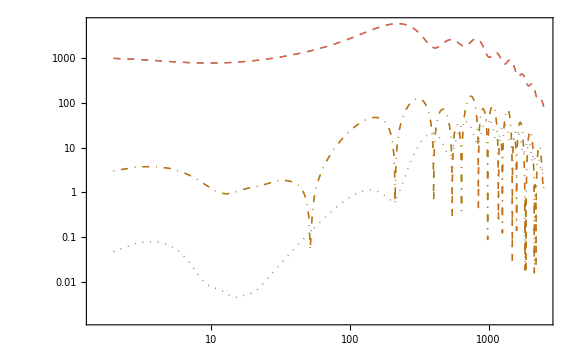

```mathematica
HDESWTT={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTHDESW;
HDESWEE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEEHDESW; 
HDESWTE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTEHDESW;
HDESBTT={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTHDESB;
HDESBEE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClEEHDESB; 
HDESBTE={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTEHDESB;
HDESSpectra=ListLogLogPlot[{HDESWTT,HDESWEE,HDESWTE,HDESWTT,HDESWEE,HDESWTE}//Evaluate,Joined->True,PlotRange->Full,Frame->True,FrameStyle->BlackFrame,PlotLabel->(MaTeX["\\textbf{HDES}",Magnification->18/12]),FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dashed],Directive[Thick,Dotted],Directive[Thick,DotDashed]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["TT"],(MaTeX[#,Magnification->1.4]&)/@Style["EE"],(MaTeX[#,Magnification->1.4]&)/@Style["TE"],(MaTeX[#,Magnification->1.4]&)/@Style["TT"],(MaTeX[#,Magnification->1.4]&)/@Style["EE"],(MaTeX[#,Magnification->1.4]&)/@Style["TE"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,1},LegendFunction->Frame],
{0.68,0.12}],ImageSize->Large]
```

The models are indistinguishable one from the other.